# Scattering Kernels in 3D

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2021 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Rayleigh Scattering

General form:

```mathematica
pRayleigh[u_,γ_]:=1/(4 Pi)3/(4(1+2γ))((1+3γ)+(1-γ)u^2)
```

Common special case (γ = 0):

```mathematica
pRayleigh[u_]:=(1+u^2)3/(16 Pi)
```

### Normalization condition

```mathematica
Integrate[2 Pi pRayleigh[u],{u,-1,1}]
```

1

```mathematica
Integrate[2 Pi pRayleigh[u,y],{u,-1,1},Assumptions->y>0]//Simplify
```

1

### Mean cosine (g)

```mathematica
Integrate[2 Pi pRayleigh[u]u,{u,-1,1}]
```

0

```mathematica
Integrate[2 Pi pRayleigh[u,y] u,{u,-1,1},Assumptions->y>0]//Simplify
```

0

### Legendre expansion coefficients

```mathematica
Integrate[2Pi(2k+1)pRayleigh[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->0,{y,0,Pi}]
```

1

```mathematica
Integrate[2Pi(2k+1)pRayleigh[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->1,{y,0,Pi}]
```

0

```mathematica
Integrate[2Pi(2k+1)pRayleigh[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->2,{y,0,Pi}]
```

1/2

### sampling

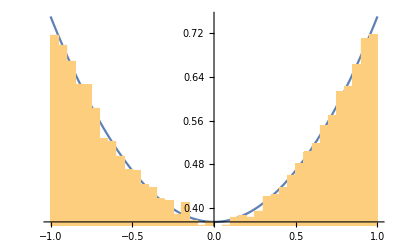

```mathematica
Show[
Plot[2 Pi pRayleigh[u],{u,-1,1}],
Histogram[Map[(1-(2-4 #+√(5+16 (-1+#)#))^(2/3))/(2-4 #+√(5+16 (-1+#) #))^(1/3)&,Table[RandomReal[],{i,1,100000}]],50,"PDF"]
]
```

Sampling strategy using 4 uniform random variates from [Mikhailov 1966, Marchuk and Mikhailov 1967]:

```mathematica
sampleMikhailov1966[]:=Module[{a,a1,a2,a3},
{a,a1,a2,a3}=RandomReal[{0,1},4];
If[0≤a≤3/4,
8/3 a-1,
Sign[a-7/8]Max[a1,a2,a3]
]
]
```

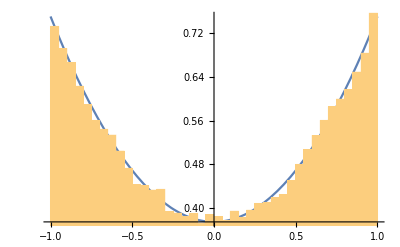

```mathematica
Show[
Plot[2 Pi pRayleigh[u],{u,-1,1}],
Histogram[Table[sampleMikhailov1966[],{i,Range[100000]}],50,"PDF"]
]
```

### Adding/doubling integrals

```mathematica
With[{l=0},
(2-KroneckerDelta[l,0])/Pi Integrate[pRayleigh[mui muo+√((1-mui^2)(1-muo^2))Cos[phi]]Cos[l phi],{phi,0,Pi},Assumptions->-1<mui<1&&-1<muo<1]

]
```

(3 (3-muo^2+mui^2 (-1+3 muo^2)))/(32 π)

```mathematica
With[{l=1},
(2-KroneckerDelta[l,0])/Pi Integrate[pRayleigh[mui muo+√((1-mui^2)(1-muo^2))Cos[phi]]Cos[l phi],{phi,0,Pi},Assumptions->-1<mui<1&&-1<muo<1]

]
```

(3 mui muo √((-1+mui^2) (-1+muo^2)))/(8 π)

```mathematica
With[{l=2},
(2-KroneckerDelta[l,0])/Pi Integrate[pRayleigh[mui muo+√((1-mui^2)(1-muo^2))Cos[phi]]Cos[l phi],{phi,0,Pi},Assumptions->-1<mui<1&&-1<muo<1]

]
```

(3 (-1+mui^2) (-1+muo^2))/(32 π)

```mathematica
With[{l=3},
(2-KroneckerDelta[l,0])/Pi Integrate[pRayleigh[mui muo+√((1-mui^2)(1-muo^2))Cos[phi]]Cos[l phi],{phi,0,Pi},Assumptions->-1<mui<1&&-1<muo<1]

]
```

0